```mathematica
f[x_]:=Exp[-a*x]*(Subscript[a, 0]+Subscript[a, 1] x+Subscript[a, 2] x^2+Subscript[a, 3] x^3);
g[x_]:=Exp[-b*x]*(Subscript[b, 0]+Subscript[b, 1] x+Subscript[b, 2] x^2+Subscript[b, 3] x^3);
```

```mathematica
LaplaceTransform[f[t],t,p]
```

a_0/(a+p)+a_1/(a+p)^2+(2 a_2)/(a+p)^3+(6 a_3)/(a+p)^4

```mathematica
LaplaceTransform[g[t],t,p]
```

b_0/(b+p)+b_1/(b+p)^2+(2 b_2)/(b+p)^3+(6 b_3)/(b+p)^4

```mathematica
FullSimplify[LaplaceTransform[f[t]*g[t],t,p]]
```

1/(a+b+p)^7((a+b+p)^3 a_0 ((a+b+p) ((a+b+p) ((a+b+p) b_0+b_1)+2 b_2)+6 b_3)+(a+b+p)^2 a_1 ((a+b+p)^3 b_0+2 (a+b+p) ((a+b+p) b_1+3 b_2)+24 b_3)+2 (a+b+p) a_2 ((a+b+p)^3 b_0+3 (a+b+p) ((a+b+p) b_1+4 b_2)+60 b_3)+6 a_3 ((a+b+p)^3 b_0+4 (a+b+p) ((a+b+p) b_1+5 b_2)+120 b_3))

```mathematica
1/(2*π*ⅈ)*Integrate[LaplaceTransform[f[t],t,s]*LaplaceTransform[g[t],t,p-s],{s,1-ⅈ*Infinity,1+ⅈ*Infinity},Assumptions->Re[a]>0,Assumptions->Re[b]>0,Assumptions->p>0]
```

ConditionalExpression[0,Re[b+p]≠0]

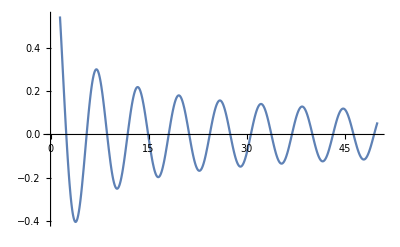

```mathematica
Plot[BesselJ[0,x],{x,0,50}]
```

```mathematica
5!
```

120

```mathematica
d[J_,m1_,m2_,theta_]:=(
lbnu=Max[m2-m1,0];
ubnu=Min[J-m1,J+m2];
nu=Range[lbnu,ubnu,1];
dPart1=Sqrt[(J+m2)!(J-m2)!(J+m1)!(J-m1)!];
dPart2=((-1)^nu(J-m1-nu)!(J+m2-nu)!(nu+m1-m2)!nu!)^-1;
dPart3=(Cos[theta/2])^(2J+m2-m1-2nu)(-Sin[theta/2])^(m1-m2+2nu);
Lnu=Length[nu];
dJm1m2=dPart1 Sum[(dPart2 dPart3)[[i]],{i,Lnu}]);
```

```mathematica
d[1,0,1,4]
```

√2 Cos[2] Sin[2]

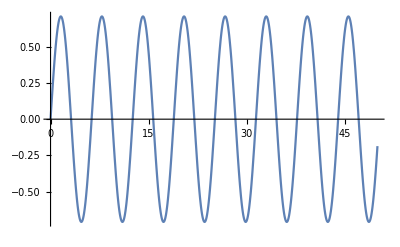

-Graphics-

```mathematica
Plot[d[1,-1,0,x],{x,0,50}]
Plot[d[1,-1,0,x],{x,0,50}]
```